## Tephigram.

Let us begin with the definitions and notations of the various variables:

pressure			: p (in Pascals (Pa))
density				: ρ (kg/m^3)
temperature			: T (Kelvin (K))
Water-vapor mass fraction	: y = ρ_v/ρ
Relative humidity		: rh = p_v/P(T)
Saturated vapor pressure	: vp

Subscripts used:
			
ambient			: amb
moist adiabat			: moist
eye				: eye
tropopause			: trop
saturated			: sat
water vapor			: v
lifting condensation level	: switch
ocean-surface value		: s
underrunning moist air		: underrun.
Tropopause			: trop

Derived Subscripts used:

staturated water vapor		: vsat
amibent ocean-surface value	: ambs
water vapor ambient		: vamb

For the purposes of generating functions and code, we will not directly make use of subscripts but rather CAPITAL letters to indicate the subscripts. So, for example, rhAMB refers to ambient relative-humidity etc.


Constants:

gravity				: g (m/s^2)
gas constant for air		: R (m^2/s^2K)
Molecular weights ratio	: σ
Specific heat capacity 		: C_p (m^2/s^2K) (at constant pressure).
Specific latent heat		: L (m^2/s^2) (phase transition)
Temperature at 0^o C in K	: T_0=273.16 K.

Let us now define the various constants. The units are taken to be in SI units.

```mathematica
Clear["Global`*"];
g = 9.81;
R = 287.1;
σ = 0.622;
cp = 1004;
L = 2.5 10^6;
T0 = 273.16;

pAMBS = 101500.0;
tAMBS = 299.0;
```

Using equation of state, we can obtain the density at the ocean surface level:

```mathematica
ρAMBS = pAMBS/(R*tAMBS)
```

1.18239

We now obtain relative humidity as a function of pressure (rh_AMB(p)) and ambient temperature as a function of pressure (T_AMB(p)) from discrete tabulated data. This data is interpolated to produce a continuous function that will be used for further computations:

```mathematica
rhAMB=Interpolation[{{101500,0.84},{100000,0.81},{95000,0.81},{90000,0.79},{85000,0.74},{80000,0.70},{75000,0.64},{70000,0.60},{65000,0.56},{60000,0.54},{55000,0.51},{50000,0.49},{45000,0.45},{40000,0.44},{30000,0.39},{20000,0.37},{10000,0.35}}];

tAMB=Interpolation[{{101500,299},{100000,299},{95000,296},{90000,293},{85000,290},{80000,288},{75000,285},{70000,282},{65000,278},{60000,274},{55000,271},{50000,266},{45000,261},{40000,255},{30000,240},{20000,218},{10000,210}}];
```

The saturated vapor pressure is computed using the following empirical formula:

p_V_SAT= 610.78 e^(a(T)(T-T_0)/(T-b(T))),
a(T) = If[T > T_0, 17.2693882, 21.8745584],
b(T) = If[T > T_0, 35.86, 7.66].

These values are obtained by performing a curvefit to data.

```mathematica
a[t_]:=If[t>T0,17.2693882,21.8745584];
b[t_]:=If[t>T0,35.86,7.66];
pVSAT[t_] = 610.78*Exp[a[t]*(t-T0)/(t-b[t])];
dpVSAT[t_] := (pVSAT[t])*(a[t])*(T0-b[t])/(t-b[t])^2;
```

#### AMBIENT PROFILES:

The ambient profiles with altitudes can be computed using equation of state:
p = ρ R T → ρ = (RT)/p, 
ρ p_v= ρ_vR T → p_v= y R T,
y = ρ_v/ρ.

```mathematica
ρAMB[p_]:= p/(R*tAMB[p]);
pVAMB[p_] := ρAMB[p]*pVSAT[p]/(R*tAMB[p]);
ρVAMB[p_]:=σ*pVAMB[p]/(R*tAMB[p]);
yAMB[p_] := ρVAMB[p]/ρAMB[p];
```

From the hydrostatic principles, using the relation (∂P)/(∂z)=-ρ g, we can compute the altitude (z) for the ambient case. The initial condition is z(P_ambs) =0. :

```mathematica
Remove[zAMB];
zAMB[p_?NumericQ]= NDSolveValue[{D[zAMB[p],p]==-1/(g*ρAMB[p]),zAMB[pAMBS]==0},zAMB[p],{p,pAMBS,10000},MaxStepSize->100,StartingStepSize->100];
```

#### MOIST ADIABAT PROFILES:

We now consider the moist adiabat profiles. We start with the thermodynamic relations between remperature and pressure:

γ = 1.4,

(T/T_ref)^(γ/(γ-1))=p/p_ref=p_v/p_v_ref, on a dry adiabat (since water vapor mass fraction (y) is constant).

Let T be the lifting-condensation level (LCL) state and left T_ref be the sea-level ambient state. 

(((T_sat)_onset)/T_ambs)^3.5=(p_vsat((T_sat)_onset))/(rh_ambs(p_ambs)p_vsat(T_ambs)).

The Temperature (T_sat)_onset can be computed using a root-finder. This gives the temperature at which the surface air would saturate if lifted dry adiabatically. The temperature implies a certain pressure on the adiabat and can be computed from the above equations.

```mathematica
tSWITCH=Block[{t},t/.FindRoot[pVSAT[t]/((t/tAMBS)^3.5)==(rhAMB[pAMBS])*(pVSAT[tAMBS]),{t,315,200}]];
pSWITCH = pAMBS*(tSWITCH/tAMBS)^3.5 ;
Print[StringForm["pLCL = `` [Pa], TLCL = `` [K]",Sequence@@(StandardForm/@{pSWITCH,tSWITCH})]]
```

pLCL = 97269.5 [Pa], TLCL = 295.385 [K]

Once saturated, the moist adiabat follows the following locus of the thrmodynamic states to rough approximation (the condensate falls out):

c_p dT + L σ d(p_vsat(T)/p) - dp/ρ = 0,
c_p dT/dp + L σ (d(p_vsat/p))/dp - RT/p = 0,
c_p dT/dp + (Lσ/p^2) (dp_vsat/dT dT/dp p-p_vsat)- RT/p = 0,
(c_p+(Lσ/p)dp_vsat/dT)dT/dp - (Lσ/p^2)p_vsat - RT/p=0.

and T(p_onset) = (T_sat)_onset

```mathematica
Remove[tmoist1];
tmoist1[p_?NumericQ]=NDSolveValue[{(cp + (L*σ/p)*dpVSAT[tmoist1[p]])*D[tmoist1[p],p] - (L*σ*pVSAT[tmoist1[p]]/p^2) - R*tmoist1[p]/p == 0,tmoist1[pSWITCH]==tSWITCH},tmoist1[p],{p,pSWITCH,10000},MaxStepSize->100, StartingStepSize->100];
```

The location at which the moist adiabat temperature matches/crosses the ambient temperature is defined as the TROPOPAUSE. The pressure at the tropopause can be found by idenfitying the pressure at which the moist adiabat temperature matches the ambient temperature. Once the pressure at the tropopause is known, the temperature and density can be computed using the ambient relationships derived earlier. The height of the tropopause can also be computed from the altitude (z) function derived earlier.

```mathematica
pTROP=Block[{p},p/.FindRoot[(tmoist1[p])-tAMB[p]==0,{p,10000,50000}]];
tTROP=tAMB[pTROP];
zTROP=zAMB[pTROP];
ρTROP=ρAMB[pTROP];

Print[StringForm["\n zTROP = `` [m], pTROP = `` [Pa], tTROP = `` [K], ρTROP = `` [kg/m^3]",Sequence@@(StandardForm/@{zTROP,pTROP,tTROP,ρTROP})]]
```

zTROP = 12692.6 [m], pTROP = 18935.5 [Pa], tTROP = 216.114 [K], ρTROP = 0.305183 [kg/m^3]

We now note that the moist-adiabat locus is based on the total energy (c_p T + Ly + gz + q^2/2 = Const.), where q^2/2 is the kinetic energy and is about 1.5% of the contribution to the total. Therefore the KE is discarded. 

Integrating from the tropopause seaward would now allow the computation of the thermodynamic states holding at the base z=0. The equation to be integrated are:

dp/dz=-ρg,
c_p dT/dz+σ L d/dZ((p_vsat(T))/p) - (1/ρ) dp/dz=0.

Since we will be integrating with respect to pressure, the equations are written as:

dz/dp = -(RT/pg),
c_p dT/dp+σ L d/dp((p_vsat(T))/p) - (RT/p) =0.

Now, we must also take into account that when pressure reaches the pressure at lifting condensation level (LCL), the terms associated with latent heat (L) drop out. In other words, when the pressure reaches the lifting condensation level, we have to switch over to dry-adiabat conditions. Taking this into account, the final form of the equations to be integrated are:

dz/dp = -(RT/pg),
(c_p+((H(p_LCL-p)Lσ)/p)dp_vsat/dT)dT/dp - ((L H(p_LCL-p)σ)/p^2)p_vsat - RT/p=0,

where H denotes the step function. However, rather than producing a discontinuous jump, an approximation of the unit step function is used to facilitate a smooth transition between the layers. The approximation used here is

H(x) ≈ 1/(1 + e^(-2 k x)) and k is a large number.  Here k = 500.

The intial conditions for altitude (z) and temperature (T) are taken to be the values at the tropopause.

```mathematica
Remove[h,zMOIST,tMOIST,temp];
h[x_]:= 1/(1+Exp[-2*500*x]);
temp = NDSolveValue[{D[zMOIST[p],p]==-(R tMOIST[p])/(p g),
(cp + (L*σ*h[pSWITCH-p]/p)*D[pVSAT[tMOIST[p]],tMOIST[p]])*D[tMOIST[p],p] - (L*σ*h[pSWITCH-p]/p^2)*pVSAT[tMOIST[p]] - R*tMOIST[p]/p == 0,
zMOIST[pTROP] == zTROP, tMOIST[pTROP]==tTROP},{zMOIST[p],tMOIST[p]},{p,pTROP,pAMBS}, MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity];
zMOIST[p_?NumericQ] = temp[[1]];
tMOIST[p_?NumericQ] = temp[[2]];
```

From these new results, we now find out the pressure at which z_Moist = 0. This  pressure and from it the temperature and pressure should be used as the next iterate to refine the results. We need to do this because we started with an assumption on the values of the pressure and temperature at the sea-level. However, these values are typically not relevant to a vertical column in the core. 

To this end, we now set up an iteration scheme to test the convergence (or divergence) of the system. The iteration scheme is set so that the average relative error between the ambient pressure and temperature at ocean surface is less than 10^-4.

```mathematica
Print["................... starting iterations....................."];
pAMBS = 101500.0;
tAMBS = 299.0;

Do[
ρAMBS = pAMBS/(R*tAMBS);

Print[StringForm["pAMBS = `` [Pa], tAMBS = `` [K], ρAMBS = `` [kg/m^3]", Sequence@@(StandardForm/@{pAMBS,tAMBS,ρAMBS})]];

Clear[zAMB];
zAMB[p_?NumericQ]= NDSolveValue[{D[zAMB[p],p]==-1/(g*ρAMB[p]),zAMB[pAMBS]==0},zAMB[p],{p,pAMBS,10000},MaxStepSize->100,StartingStepSize->100];

tSWITCH=Block[{t},t/.FindRoot[pVSAT[t]/((t/tAMBS)^3.5)==(rhAMB[pAMBS])*(pVSAT[tAMBS]),{t,315,200}]];
pSWITCH = pAMBS*(tSWITCH/tAMBS)^3.5 ;
Print[StringForm["pLCL = `` [Pa], TLCL = `` [K]",Sequence@@(StandardForm/@{pSWITCH,tSWITCH})]];

Clear[tmoist1];
tmoist1[p_?NumericQ]=NDSolveValue[{(cp + (L*σ/p)*dpVSAT[tmoist1[p]])*D[tmoist1[p],p] - (L*σ*pVSAT[tmoist1[p]]/p^2) - R*tmoist1[p]/p == 0,tmoist1[pSWITCH]==tSWITCH},tmoist1[p],{p,pSWITCH,10000},MaxStepSize->100, StartingStepSize->100];

pTROP=Block[{p},p/.FindRoot[(tmoist1[p])-tAMB[p]==0,{p,10000,50000}]];
tTROP=tAMB[pTROP];
zTROP=zAMB[pTROP];
ρTROP=ρAMB[pTROP];

Print[StringForm["zTROP = `` [m], pTROP = `` [Pa], tTROP = `` [K], ρTROP = `` [kg/m^3]",Sequence@@(StandardForm/@{zTROP,pTROP,tTROP,ρTROP})]];

Clear[zMOIST,tMOIST];
temp = NDSolveValue[{D[zMOIST[p],p]==-(R tMOIST[p])/(p g),
(cp + (L*σ*h[pSWITCH-p]/p)*dpVSAT[tMOIST[p]])*D[tMOIST[p],p] - (L*σ*h[pSWITCH-p]/p^2)*pVSAT[tMOIST[p]] - R*tMOIST[p]/p == 0,
zMOIST[pTROP] == zTROP, tMOIST[pTROP]==tTROP},{zMOIST[p],tMOIST[p]},{p,pTROP,pAMBS}, MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity];

zMOIST[p_?NumericQ] = temp[[1]];
tMOIST[p_?NumericQ] = temp[[2]];

pAMBS1 = Block[{p},p/.Quiet@FindRoot[zMOIST[p]==0,{p,pAMBS}]];
tAMBS1 = tMOIST[pAMBS1];

avgRelativeError = (Abs[(pAMBS1-pAMBS)/pAMBS]+ Abs[(tAMBS1-tAMBS)/tAMBS])/2;
Print["average err ->", avgRelativeError];

If[avgRelativeError < 10^-4, Break[]];

Print["err pAMBS->",Abs[(pAMBS1-pAMBS)/pAMBS]];
Print["err tAMBS ->", Abs[(tAMBS1-tAMBS)/tAMBS]]; 
pAMBS = pAMBS1;
tAMBS = tAMBS1;

Print[StringForm["............... iteration ->  `1` done....................", iter]];
,{iter,30}
];

Print["final result -->"];
Print[StringForm["pAMBS = `` [Pa], tAMBS = `` [K], ρAMBS = `` [kg/m^3]", Sequence@@(StandardForm/@{pAMBS,tAMBS,ρAMBS})]];
```

................... starting iterations.....................

pAMBS = 101500. [Pa], tAMBS = 299. [K], ρAMBS = 1.18239 [kg/m^3]

pLCL = 97269.5 [Pa], TLCL = 295.385 [K]

zTROP = 12692.6 [m], pTROP = 18935.5 [Pa], tTROP = 216.114 [K], ρTROP = 0.305183 [kg/m^3]

average err ->0.0106307

err pAMBS->0.0165196

err tAMBS ->0.00474175

............... iteration ->  1 done....................

pAMBS = 99823.3 [Pa], tAMBS = 297.582 [K], ρAMBS = 1.1684 [kg/m^3]

pLCL = 94801.3 [Pa], TLCL = 293.226 [K]

zTROP = 11640.9 [m], pTROP = 21814.7 [Pa], tTROP = 221.567 [K], ρTROP = 0.342935 [kg/m^3]

average err ->0.00307752

err pAMBS->0.00479423

err tAMBS ->0.0013608

............... iteration ->  2 done....................

pAMBS = 99344.7 [Pa], tAMBS = 297.177 [K], ρAMBS = 1.16438 [kg/m^3]

pLCL = 94225.6 [Pa], TLCL = 292.719 [K]

zTROP = 11274.3 [m], pTROP = 22928.7 [Pa], tTROP = 223.931 [K], ρTROP = 0.356642 [kg/m^3]

average err ->0.00152235

err pAMBS->0.00237715

err tAMBS ->0.000667548

............... iteration ->  3 done....................

pAMBS = 99108.5 [Pa], tAMBS = 296.979 [K], ρAMBS = 1.16239 [kg/m^3]

pLCL = 93958.9 [Pa], TLCL = 292.486 [K]

zTROP = 11060. [m], pTROP = 23613.2 [Pa], tTROP = 225.433 [K], ρTROP = 0.364841 [kg/m^3]

average err ->0.000845873

err pAMBS->0.00132546

err tAMBS ->0.00036629

............... iteration ->  4 done....................

pAMBS = 98977.2 [Pa], tAMBS = 296.87 [K], ρAMBS = 1.16128 [kg/m^3]

pLCL = 93815.2 [Pa], TLCL = 292.362 [K]

zTROP = 10923.9 [m], pTROP = 24062.1 [Pa], tTROP = 226.435 [K], ρTROP = 0.370131 [kg/m^3]

average err ->0.000500636

err pAMBS->0.000788687

err tAMBS ->0.000212584

............... iteration ->  5 done....................

pAMBS = 98899.1 [Pa], tAMBS = 296.807 [K], ρAMBS = 1.16061 [kg/m^3]

pLCL = 93731.2 [Pa], TLCL = 292.29 [K]

zTROP = 10835.6 [m], pTROP = 24359. [Pa], tTROP = 227.104 [K], ρTROP = 0.373595 [kg/m^3]

average err ->0.000310919

err pAMBS->0.000493634

err tAMBS ->0.000128204

............... iteration ->  6 done....................

pAMBS = 98850.3 [Pa], tAMBS = 296.769 [K], ρAMBS = 1.16018 [kg/m^3]

pLCL = 93679.2 [Pa], TLCL = 292.248 [K]

zTROP = 10778.3 [m], pTROP = 24553.8 [Pa], tTROP = 227.546 [K], ρTROP = 0.375852 [kg/m^3]

average err ->0.00020225

err pAMBS->0.000324652

err tAMBS ->0.000079847

............... iteration ->  7 done....................

pAMBS = 98818.2 [Pa], tAMBS = 296.745 [K], ρAMBS = 1.1599 [kg/m^3]

pLCL = 93645.2 [Pa], TLCL = 292.221 [K]

zTROP = 10741.4 [m], pTROP = 24679.7 [Pa], tTROP = 227.832 [K], ρTROP = 0.377305 [kg/m^3]

average err ->0.000138413

err pAMBS->0.00022538

err tAMBS ->0.0000514458

............... iteration ->  8 done....................

pAMBS = 98795.9 [Pa], tAMBS = 296.73 [K], ρAMBS = 1.1597 [kg/m^3]

pLCL = 93621.7 [Pa], TLCL = 292.204 [K]

zTROP = 10717.8 [m], pTROP = 24760. [Pa], tTROP = 228.015 [K], ρTROP = 0.378229 [kg/m^3]

average err ->0.000100447

err pAMBS->0.000166337

err tAMBS ->0.000034558

............... iteration ->  9 done....................

pAMBS = 98779.5 [Pa], tAMBS = 296.72 [K], ρAMBS = 1.15954 [kg/m^3]

pLCL = 93604.4 [Pa], TLCL = 292.193 [K]

zTROP = 10702.6 [m], pTROP = 24811. [Pa], tTROP = 228.131 [K], ρTROP = 0.378815 [kg/m^3]

average err ->0.0000775877

final result -->

pAMBS = 98779.5 [Pa], tAMBS = 296.72 [K], ρAMBS = 1.15954 [kg/m^3]

From the above iteration scheme it can be seen that the solution converges in 10 iterations.

#### EYE ADIABAT PROFILES:

Let us assume that the underrun happens at a certain pressure, say, p = 80000.00 Pa. The following equations are integrated from the tropopause to the surface and the height at which the underrun is computed:

dz/dp = -(RT/pg),
c_p dT/dp+σ L RH d/dp((p_vsat(T))/p) - (RT/p) =0,
p(ztrop) = ptrop, T(ztrop) = Ttrop.

In the above system, we have a new term RH (relative humiidty) which takes on a value 0≤ RH ≤1. 

If RH=0, then the eye is totally dry. In this case, the pressure at sea-level is quite decremented from the ambient pressure at the surface. 
If RH=1, all the heating in the eyewall owing to condensation is revered in the eye owing to evaporation.

```mathematica
Remove[eyeProfiles];
eyeProfiles[pUnderrun_?NumericQ, RH_?NumericQ]:= Module[{temp, p, zEYE,tEYE,ρEYE},
temp = NDSolveValue[{D[zEYE[p],p]==-(R tEYE[p])/(p g),
(cp + (L*σ*RH/p)*dpVSAT[tEYE[p]])*D[tEYE[p],p] - (L*σ*RH/p^2)*pVSAT[tEYE[p]] - R*tEYE[p]/p == 0,
zEYE[pTROP] == zTROP, tEYE[pTROP]==tTROP},{zEYE[p],tEYE[p]},{p,pTROP,pAMBS}, MaxStepSize->100,StartingStepSize->100,AccuracyGoal->Infinity];
zEYE= Function@@List[p,temp[[1]]];
tEYE = Function@@List[p, temp[[2]]];
ρEYE= Function@@List[p, p/(R*tEYE[p])];
{zEYE,tEYE,ρEYE}
];
```

Let us look at the case when RH = 0.

```mathematica
Remove[zEYE,tEYE,ρEYE];
{zEYE,tEYE,ρEYE} = eyeProfiles[80000.0, 0.];
StringForm["Ambient surface pressure = `1` Pa.,\nPressure when RH=0 at z=0 -> `2` Pa", pAMBS,p/.FindRoot[zEYE[p]==0,{p,pAMBS}]]
```

Ambient surface pressure = 98779.5 Pa.,
Pressure when RH=0 at z=0 -> 92837.1 Pa

We can clearly see that the pressure is decremented for this case. Now let us look at the case when RH =

```mathematica
{zEYE,tEYE,ρEYE} = eyeProfiles[80000.0, 0.65];
zEYE[pAMBS]
```

-96.0935

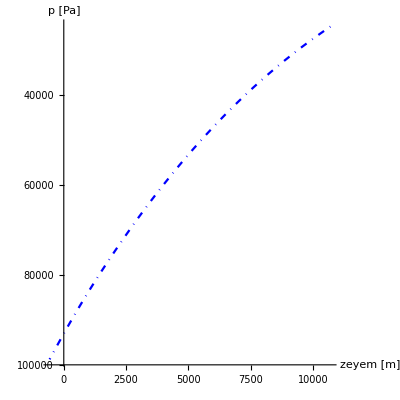

```mathematica
ParametricPlot[{zEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"zeyem [m]","p [Pa]"}, PlotRange->All,AspectRatio->1,ScalingFunctions->{Identity,"Reverse"}, PlotStyle->{{Blue,DotDashed}}]
```

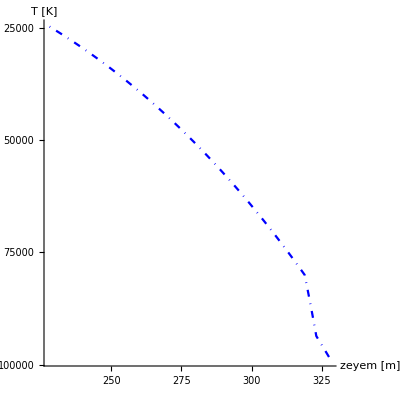

```mathematica
ParametricPlot[{tEYE[p],p},{p,pAMBS,pTROP},AxesLabel->{"zeyem [m]","T [K]"}, PlotRange->All,AspectRatio->1,ScalingFunctions->{Identity,"Reverse"}, PlotStyle->{{Blue,DotDashed}},AxesOrigin->{200,10000}]
```